```mathematica
Micro-magnet B field calculations
```

This notebook is used to specify the design of a simple micro-magnet and calculate the magnetic fields using the Radia package.

```mathematica
<<Radia`;
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

In all calculations,  I will calculate the B-field in a 200nm x 200nm region in the plane of the donors. This is a convention I am following and there is no specific reason for chosing these dimensions. In fact, a possible followup could be to optimze over the size of micromagnets (Machine Learning?) for the largest number of qubits. With this being written, this will be another paper and not this one.

## Simple Square Micro-magnet

We first consider a micromagnet design with a single top magnet over the donor plane. The dimensions of the micromagnet are assumed to be 500 nm x 500 nm x 100nm. The donors are assumed to be present at z = 0 plane. The micromagnet is located at 50nm above the donors.

```mathematica
(* All units are in mm*)
depthDonor = 50 10^-6;
lengthMagnet = 200 10^-6;
yRange = 200 10^-6;
heightMagnet = 100 10^-6;
(* The height of the magnet used in Scarlino's thesis was 200nm*)

magVector = {1,0,0}; (* Magnetisation vector of the magnet, units are SI units *)

(*Note that the position of the centre of the cuboid is specified. Hence the finite height of the micromagnet has to taken into account while specifiying the position*)
magnet = radObjRecMag[{0,0,depthDonor + heightMagnet/2},{lengthMagnet,yRange,heightMagnet},magVector];
magnetContainer = radObjCnt[{magnet}];

Show[Graphics3D[radObjDrw[magnetContainer]]]
```

-Graphics3D-

Once the micromagnet geometry has been defined, it is very easy to produce magnetic field maps. Here, the magnet field components are plotted in the donor (z=0) plane.

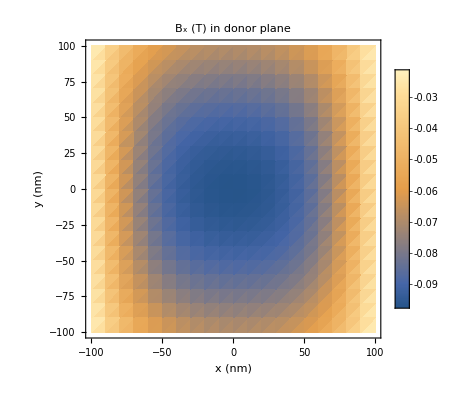

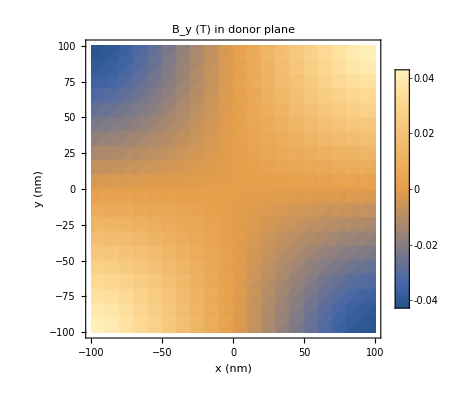

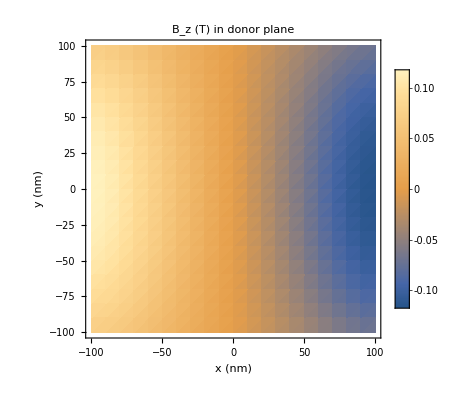

```mathematica
(*Discretisation in x and y*)
dx = 10 10^-6;
dy = 10 10^-6;

bx = Transpose[Table[radFld[magnetContainer,"bx",{x,y,0}],{x,-lengthMagnet/2,lengthMagnet/2,dx},{y,-yRange/2,yRange/2,dy}]];
by = Transpose[Table[radFld[magnetContainer,"by",{x,y,0}],{x,-lengthMagnet/2,lengthMagnet/2,dx},{y,-yRange/2,yRange/2,dy}]];
bz = Transpose[Table[radFld[magnetContainer,"bz",{x,y,0}],{x,-lengthMagnet/2,lengthMagnet/2,dx},{y,-yRange/2,yRange/2,dy}]];

ListDensityPlot[bx,FrameLabel->{"x (nm)","y (nm)"},DataRange -> {{-lengthMagnet/2 *10^6,lengthMagnet/2*10^6},{-yRange/2*10^6,yRange/2*10^6}},PlotLegends->Automatic,PlotLabel-> "B_x (T) in donor plane"]
ListDensityPlot[by,FrameLabel->{"x (nm)","y (nm)"},DataRange -> {{-lengthMagnet/2 *10^6,lengthMagnet/2*10^6},{-yRange/2*10^6,yRange/2*10^6}},PlotLegends->Automatic,PlotLabel-> "B_y (T) in donor plane"]
ListDensityPlot[bz,FrameLabel->{"x (nm)","y (nm)"},DataRange -> {{-lengthMagnet/2 *10^6,lengthMagnet/2*10^6},{-yRange/2*10^6,yRange/2*10^6}},PlotLegends->Automatic,PlotLabel-> "B_z (T) in donor plane"]
```

Data is exported to ASCII files which can be read by Python.

```mathematica
Export["~/repos/donor-micromagnet-arch/code/B field data/Bx_simple.dat",bx];
Export["~/repos/donor-micromagnet-arch/code/B field data/By_simple.dat",by];
Export["~/repos/donor-micromagnet-arch/code/B field data/Bz_simple.dat",bz];
```

# Two Square Micro-magnets

We now cosider a geometry wherein the donors are located between the poles of two micromagnets.

```mathematica
(* All units are in mm*)
depth2DEG = 50 10^-6;

lengthMagnet = 200 10^-6;
yRange = 200 10^-6;
heightMagnet = 100 10^-6;

distanceMagnets = 400 10^-6; (*the distance is measured from centre to centre*)
magVector = {1,0,0}; (* Magnetisation vector of the magnet, units are SI units *)
magnet1 = radObjRecMag[{-distanceMagnets/2 ,0,depth2DEG + heightMagnet/2},{lengthMagnet,yRange,heightMagnet},magVector];
magnet2 = radObjRecMag[{distanceMagnets /2,0,depth2DEG + heightMagnet/2},{lengthMagnet,yRange,heightMagnet},magVector];
magnetContainer = radObjCnt[{magnet1,magnet2}];

Show[Graphics3D[radObjDrw[magnetContainer]]]
```

-Graphics3D-

Once the micromagnet geometry has been defined, it is very easy to produce magnetic field maps. Here, the magnet field components are plotted in the 2DEG plane.

```mathematica
(*Discretisation in x and y*)
dx = 1 10^-6;
dy = 1 10^-6;

xRange = distanceMagnets/2 - lengthMagnet/2;
bx =  Transpose[Table[radFld[magnetContainer,"bx",{x,y,0}],{x,-xRange,xRange,dx},{y,-yRange/2,yRange/2,dy}]];
by =  Transpose[Table[radFld[magnetContainer,"by",{x,y,0}],{x,-xRange,xRange,dx},{y,-yRange/2,yRange/2,dy}]];
bz =  Transpose[Table[radFld[magnetContainer,"bz",{x,y,0}],{x,-xRange,xRange,dx},{y,-yRange/2,yRange/2,dy}]];

ListDensityPlot[bx,FrameLabel->{"x (nm)","y (nm)"},DataRange -> {{-lengthMagnet *10^6,lengthMagnet*10^6},{-yRange*10^6,yRange*10^6}},PlotLegends->Automatic,PlotLabel-> "B_x (T) in donor Plane"]
ListDensityPlot[by,FrameLabel->{"x (nm)","y (nm)"},DataRange -> {{-lengthMagnet *10^6,lengthMagnet*10^6},{-yRange*10^6,yRange*10^6}},PlotLegends->Automatic,PlotLabel-> "B_y (T) in donor Plane"]
ListDensityPlot[bz,FrameLabel->{"x (nm)","y (nm)"},DataRange -> {{-lengthMagnet *10^6,lengthMagnet*10^6},{-yRange*10^6,yRange*10^6}},PlotLegends->Automatic,PlotLabel-> "B_z (T) in donor Plane"]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Export["~/repos/donor-micromagnet-arch/code/B field data/Bx_two.dat",bx];
Export["~/repos/donor-micromagnet-arch/code/B field data/By_two.dat",by];
Export["~/repos/donor-micromagnet-arch/code/B field data/Bz_two.dat",bz];
```

## Slanting Micromagnet

We now consider a different geometry wherein the magnets are placed in a direction perpendicular to the line along which the dots are present. One of the micromagnets in given a slanting shape in order to achieve better gradients.

```mathematica
(* All units are in mm*)
depthDonor = 50 10^-6;

lengthMagnet = 200 10^-6;
yRange = 200 10^-6;
heightMagnet = 100 10^-6;

distanceMagnets = 400 10^-6;
dxMag = lengthMagnet/8;
dyMag = yRange/4;

magUp = radObjRecMag[{0,distanceMagnets/2,depthDonor + heightMagnet/2},{lengthMagnet,yRange,heightMagnet},{1,0,0}];
magDown1 = radObjRecMag[{-2*dxMag,-distanceMagnets/2 +dyMag,depthDonor + heightMagnet/2},{4*dxMag,dyMag,heightMagnet},{1,0,0}];
magDown2 = radObjRecMag[{ -dxMag,-distanceMagnets/2 ,depthDonor + heightMagnet/2},{6*dxMag,dyMag,heightMagnet},{1,0,0}];
magDown3 = radObjRecMag[{0,-distanceMagnets/2 - 1.5*dyMag,depthDonor + heightMagnet/2},{8*dxMag,2*dyMag,heightMagnet},{1,0,0}];

magnetContainer =radObjCnt[{magUp,magDown1,magDown2,magDown3}];
Show[Graphics3D[radObjDrw[magnetContainer]]]
```

-Graphics3D-

```mathematica
(*Discretisation in x and y*)
dx = 1 10^-6;
dy = 1 10^-6;

xRange = distanceMagnets/2 - lengthMagnet/2;
bx =  Transpose[Table[radFld[magnetContainer,"bx",{x,y,0}],{x,-xRange,xRange,dx},{y,-yRange/2,yRange/2,dy}]];
by =  Transpose[Table[radFld[magnetContainer,"by",{x,y,0}],{x,-xRange,xRange,dx},{y,-yRange/2,yRange/2,dy}]];
bz =  Transpose[Table[radFld[magnetContainer,"bz",{x,y,0}],{x,-xRange,xRange,dx},{y,-yRange/2,yRange/2,dy}]];

ListDensityPlot[bx,FrameLabel->{"x (nm)","y (nm)"},DataRange -> {{-lengthMagnet *10^6,lengthMagnet*10^6},{-yRange*10^6,yRange*10^6}},PlotLegends->Automatic,PlotLabel-> "B_x (T) in donor Plane"]
ListDensityPlot[by,FrameLabel->{"x (nm)","y (nm)"},DataRange -> {{-lengthMagnet *10^6,lengthMagnet*10^6},{-yRange*10^6,yRange*10^6}},PlotLegends->Automatic,PlotLabel-> "B_y (T) in donor Plane"]
ListDensityPlot[bz,FrameLabel->{"x (nm)","y (nm)"},DataRange -> {{-lengthMagnet *10^6,lengthMagnet*10^6},{-yRange*10^6,yRange*10^6}},PlotLegends->Automatic,PlotLabel-> "B_z (T) in donor Plane"]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Export["~/repos/donor-micromagnet-arch/code/B field data/Bx_slant.dat",bx];
Export["~/repos/donor-micromagnet-arch/code/B field data/By_slant.dat",by];
Export["~/repos/donor-micromagnet-arch/code/B field data/Bz_slant.dat",bz];
```

```mathematica
Array of Slanting Magnets
	In order to achieve scalabilty, I will investigate a setup in which the slanting micromagnet architecture will be repeated a given number of times. Both cases of inplane and out of plane magnetisation will be analysed.
```

```mathematica
In plane magnetisation
```

```mathematica
numMag =1; (* number of magnets on each side of the origin *)
(* All units are in mm*)
depthDonor = 50 10^-6;
lengthMagnet = 200 10^-6;
yRange = 200 10^-6;
heightMagnet = 100 10^-6;

distanceMagnets = 400 10^-6;
dxMag = lengthMagnet;
dyMag = yRange/4;

magUp = Table[radObjRecMag[{i*dxMag,distanceMagnets/2,depthDonor + heightMagnet/2},{lengthMagnet,yRange,heightMagnet},{1,0,0}],{i,-numMag,numMag}];;
magDown1 = Table[radObjRecMag[{i*dxMag,-distanceMagnets/2 +dyMag,depthDonor + heightMagnet/2},{4*dxMag/8,dyMag,heightMagnet},{1,0,0}],{i,-numMag,numMag}];
(*magDown2 = Table[radObjRecMag[{ i*dxMag,-distanceMagnets/2 ,depthDonor + heightMagnet/2},{6*dxMag/8,dyMag,heightMagnet},{1,0,0}],{i,-numMag,numMag}];
magDown3 = Table[radObjRecMag[{i*dxMag,-distanceMagnets/2 - 1.5*dyMag,depthDonor + heightMagnet/2},{8*dxMag/8,2*dyMag,heightMagnet},{1,0,0}],{i,-numMag,numMag}];*)


magnetContainer =radObjCnt[Catenate[{magDown1}]];
Show[Graphics3D[radObjDrw[magnetContainer]]]
```

-Graphics3D-

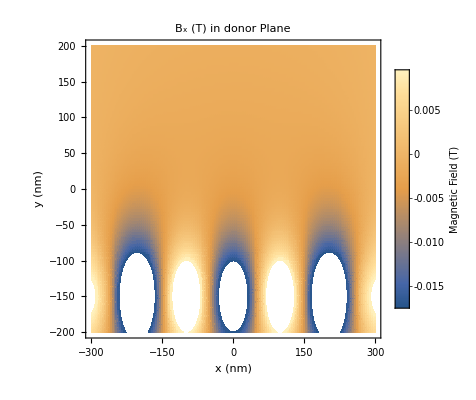

-Graphics-

-Graphics-

```mathematica
(*Discretisation in x and y*)
numPoints = 100;
dx = (numMag+1)*dxMag/numPoints;
dy =distanceMagnets/numPoints;

xRange = numMag*dxMag + lengthMagnet/2;
yRange =distanceMagnets/2;
bx =  Table[radFld[magnetContainer,"bx",{x,y,0}],{y,-yRange,yRange,dy},{x,-xRange,xRange,dx}];
by =  Table[radFld[magnetContainer,"by",{x,y,0}],{y,-yRange,yRange,dy},{x,-xRange,xRange,dx}];
bz =  Table[radFld[magnetContainer,"bz",{x,y,0}],{y,-yRange,yRange,dy},{x,-xRange,xRange,dx}];

ListDensityPlot[bx,FrameLabel->{"x (nm)","y (nm)"},DataRange -> {{-xRange*10^6,xRange*10^6},{-yRange*10^6,yRange*10^6}},PlotLabel-> "B_x (T) in donor Plane",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Magnetic Field (T)",LabelStyle->{Italic,FontFamily->"Helvetica"}],Right]]
ListDensityPlot[by,FrameLabel->{"x (nm)","y (nm)"},DataRange -> {{-xRange *10^6,xRange*10^6},{-yRange*10^6,yRange*10^6}},PlotLabel-> "B_y (T) in donor Plane",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Magnetic Field (T)",LabelStyle->{Italic,FontFamily->"Helvetica"}],Right]]
ListDensityPlot[bz,FrameLabel->{"x (nm)","y (nm)"},DataRange -> {{-xRange*10^6,xRange*10^6},{-yRange*10^6,yRange*10^6}},PlotLabel-> "B_z (T) in donor Plane",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Magnetic Field (T)",LabelStyle->{Italic,FontFamily->"Helvetica"}],Right]]
```

```mathematica
-Graphics-
Export["~/repos/donor-micromagnet-arch/code/B field data/Bx_slant.dat",bx];
Export["~/repos/donor-micromagnet-arch/code/B field data/By_slant.dat",by];
Export["~/repos/donor-micromagnet-arch/code/B field data/Bz_slant.dat",bz];
```

-Graphics-

```mathematica
Out of plane magnetisation
```

```mathematica
numMag =3; (* number of magnets on each side of the origin *)
(* All units are in mm*)
depthDonor = 50 10^-6;
lengthMagnet = 200 10^-6;
yRange = 200 10^-6;
heightMagnet = 100 10^-6;

distanceMagnets = 400 10^-6;
dxMag = lengthMagnet;
dyMag = yRange/4;

magUp = Table[radObjRecMag[{i*dxMag,distanceMagnets/2,depthDonor + heightMagnet/2},{lengthMagnet,yRange,heightMagnet},{0,0,1}],{i,-numMag,numMag}];;
magDown1 = Table[radObjRecMag[{i*dxMag,-distanceMagnets/2 +dyMag,depthDonor + heightMagnet/2},{4*dxMag/8,dyMag,heightMagnet},{0,0,1}],{i,-numMag,numMag}];
magDown2 = Table[radObjRecMag[{ i*dxMag,-distanceMagnets/2 ,depthDonor + heightMagnet/2},{6*dxMag/8,dyMag,heightMagnet},{0,0,1}],{i,-numMag,numMag}];
magDown3 = Table[radObjRecMag[{i*dxMag,-distanceMagnets/2 - 1.5*dyMag,depthDonor + heightMagnet/2},{8*dxMag/8,2*dyMag,heightMagnet},{0,0,1}],{i,-numMag,numMag}];

magnetContainer =radObjCnt[Catenate[{magUp,magDown1,magDown2,magDown3}]];
Show[Graphics3D[radObjDrw[magnetContainer]]]
```

-Graphics3D-

```mathematica
(*Discretisation in x and y*)
numPoints = 100;
dx = numMag*dxMag/numPoints;
dy =distanceMagnets/numPoints;

xRange = numMag*dxMag + lengthMagnet/2;
yRange = yRange/2;
bx =  Table[radFld[magnetContainer,"bx",{x,y,0}],{y,-yRange/2,yRange/2,dy},{x,-xRange,xRange,dx}];
by =  Table[radFld[magnetContainer,"by",{x,y,0}],{y,-yRange/2,yRange/2,dy},{x,-xRange,xRange,dx}];
bz =  Table[radFld[magnetContainer,"bz",{x,y,0}],{y,-yRange/2,yRange/2,dy},{x,-xRange,xRange,dx}];

ListDensityPlot[bx,FrameLabel->{"x (nm)","y (nm)"},DataRange -> {{-xRange*10^6,xRange*10^6},{-yRange*10^6,yRange*10^6}},PlotLabel-> "B_x (T) in donor Plane",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Magnetic Field (T)",LabelStyle->{Italic,FontFamily->"Helvetica"}],Right]]
ListDensityPlot[by,FrameLabel->{"x (nm)","y (nm)"},DataRange -> {{-xRange *10^6,xRange*10^6},{-yRange*10^6,yRange*10^6}},PlotLabel-> "B_y (T) in donor Plane",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Magnetic Field (T)",LabelStyle->{Italic,FontFamily->"Helvetica"}],Right]]
ListDensityPlot[bz,FrameLabel->{"x (nm)","y (nm)"},DataRange -> {{-xRange*10^6,xRange*10^6},{-yRange*10^6,yRange*10^6}},PlotLabel-> "B_z (T) in donor Plane",PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"Magnetic Field (T)",LabelStyle->{Italic,FontFamily->"Helvetica"}],Right]]
```

-Graphics-

-Graphics-

-Graphics-